# Математическое моделирование и сложные процессы.

## Лабораторная работа №1 Моделирование поведения толпы методом конечных автоматов.

Лицкевич В.Л.

# Задание

⁃Graphics⁃

Задача: Задан тоннель. Ширина 21 клетка на входе и 7 клеток на выходе. В тоннель прибывают люди со скоростью 11 чел за такт. Каждый человек стремится к выходу из тоннеля. Каждый человек видит ситуацию на 3 клетки в каждую сторону.
Весовые коэффициенты предпочтения движения в данном направлении определяются в зависимотсти от колличества свободных клеток ({0} | {1} | {2} | {3}
0. | 0.5 | 0.75 | 1.), и в зависимости от выгодности направления движения по следующим формулам:

```mathematica
(*Тенденция движения:{N,E,S,W} d-дирекционный синус:N=(d^2+1/3)/If[d<0,1,3,1];
E=1-d^2;
S=(d^2+1/3)/If[d>0,1,3,1];
W=((d^2+1/3))/6;*)
```

Решение о передвижении в направлениях {N,E,S,W} принимается случайным образом,на основе препочтений каждого участника численного эксперимента.

Задание 1. Построить симуляционную модель, провести возможные оптимизации. Сделать анимацию процесса продолжительностью в 100 тактов.

Задание 2. Запрограммировать численный эксперимент длинной в 1000 тактов. Построить графики колличества вошедших и вышедших за такт. (Ширина сужения 7 клеток)

Задание 3. Провести численный эксперимент для всех сужений от 0 до 15 клеток шириной, и выяснить оптимальную ширину сужения тоннеля относительно предотвращения образования пробок.

```mathematica
Tunnel[length_,constriction_]:=Module[{InW=21, OutW=7,T,TrT,i},
T=Table[0,{i,1,InW},{j,1,length}];
T⟦1⟧=T⟦-1⟧=Table[1,{i,1,length}];
TrT=Transpose@T;
TrT⟦1⟧=Table[1,{i,1,InW}];
For[i=1,i≤15-constriction,
TrT⟦-i,1;;OutW⟧=TrT⟦-i,InW-OutW+1;;InW⟧=1;i++];
For[i=15-OutW+1,i≤15,
TrT⟦-i,1;;OutW-(i-OutW-2)⟧=TrT⟦-i,InW-OutW+1+(i-OutW-2);;InW⟧=1;i++];
Transpose@TrT]
DisplayTunnel[Tunnel_]:=Graphics[Table[Which[Tunnel⟦i,j⟧==0,{EdgeForm[Thick],White,Rectangle[{j,i}]}, Tunnel⟦i,j⟧==1,{EdgeForm[Thick],Orange,Rectangle[{j,i}]}, Tunnel⟦i,j⟧==2,{EdgeForm[Thick],Red,Rectangle[{j,i}]}],{i,1,Length@Tunnel}, {j,1,Length@Tunnel⟦1⟧}]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

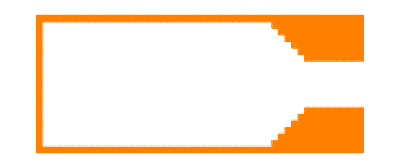

```mathematica
T=Tunnel[50,7]
DisplayTunnel[T]
```

```mathematica
Arr[Tunnel_]:=Module[{F, T=Tunnel,Em,New,i},
F= T⟦;;,2⟧;
Em=DeleteCases[Table[If[F⟦i⟧==0,i],{i,1,Length@F}],Null];
New = If[Length@Em≥11,RandomSample[Em,11],Em];
For[i=1,i≤Length@New,
	T⟦New⟦i⟧,2⟧=2;
	i++];
T
]
```

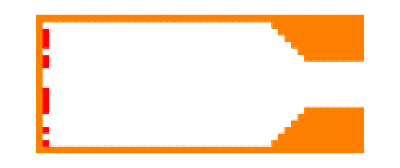

```mathematica
DisplayTunnel[T=Arr@T]
```

```mathematica
Move[Tunnel_]:=Module[{},]
```